# RQA Exploration

Alison Ord

Flip Phillips

## To do notes

6 July 2019
* Find out why some of the stuff working yesterday afternoon wasn’t working come evening!
* Try to obtain numbers for the RQA’s instead of the timeseries boxes - you seem to have got the right number of boxes
* Plot the numbers against the value of the timeseries - and modify the existing plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch
* Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?
* Consider Meredith’s code for a moving window collecting data during loading, and throwing away the data until their chosen event occurs, and then retaining the immediately prior windows, and then windows during and after the event.

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

The package is built on the equations expressed in Webber and Marwan (2015).

## Find and load the data

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

We start by using the data from the same folded rock to which we applied the nonlinear tools of spatial attractor, wavelet transform (2D and 3D), Hurst exponents, singularity spectrum (not yet in mtca), and so on.

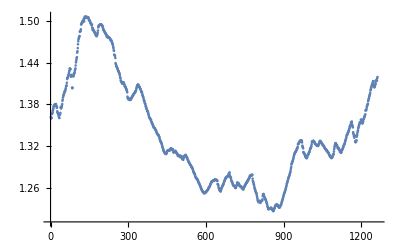

```mathematica
ListPlot[data]
```

We create a time series in the form required by mtca.

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

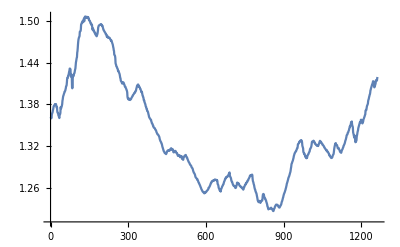

```mathematica
ListLinePlot[ds]
```

Trial some predictions based on existing mtca functions

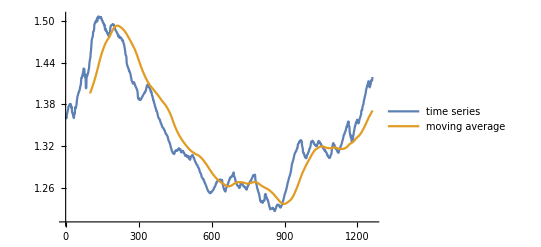

```mathematica
avg=MovingAverage[ds,100];
ListLinePlot[{ds,avg},PlotLegends->{"time series","moving average"}]
```

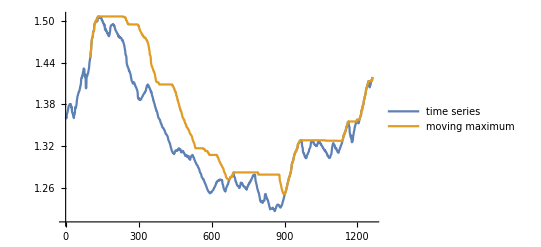

```mathematica
max=MovingMap[Max,ds,100];
ListLinePlot[{ds,max},PlotLegends->{"time series","moving maximum"}]
```

```mathematica
dsm=TimeSeriesModelFit[ds]
```

TimeSeriesModel[…]

Use TimeSeriesForecastpaclet:ref/TimeSeriesForecast to forecast the next 1000 values in the time series:

```mathematica
dsf=TimeSeriesForecast[dsm,{1000}];
```

Plot the time series along with the forecast:

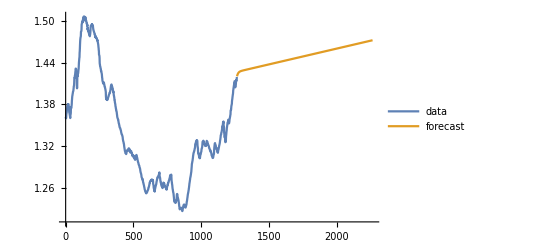

```mathematica
ListLinePlot[{ds,dsf},PlotLegends->{"data","forecast"}]
```

```mathematica
eproc=TimeSeriesModelFit[ds,{"SARIMA",12}]["Process"]
```

SARIMAProcess[-2.37682×10^-7,{0.41765,0.19998},1,{},{12,{-0.0917179},1,{-0.846865}},2.3812×10^-6]

```mathematica
forecast=TimeSeriesForecast[eproc,ds,{1000}];
```

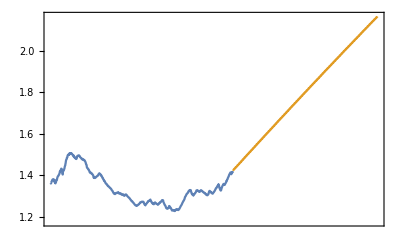

```mathematica
DateListPlot[{ds,forecast},Joined->True]
```

## Estimate the lag and embedding dimensions for the data

The lag is first estimated-

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

However, a lag of 10 was used in previously published work (Ord&Hobbs, 2018; Ord et al., 2018) so that is what we will use here.

```mathematica
lag=10
```

10

The embedding dimension of the system is then estimated. The result below suggests a dimension of 3.

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.40655,1262,4.72984×10^-8,1252,1.41325×10^-6},{3,0.0990338,1252,1.41325×10^-6,1242,2.94388×10^-6},{4,0.023539,1242,2.94388×10^-6,1232,4.36527×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

What do I have to do to read these numbers?

## Plot the 3D spatial attractor

embedding is now a list of 3 columns of data, off set by the lag of 10, and we plot these in three dimensions, with the axes representing t, t+10, t+20

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]},ViewPoint->{Left,Top}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]],ViewPoint->{Left,Bottom}]
```

-Graphics3D-

These give you information on the neighbours, nearestneighbours and neighbours, but what is it you really need to know? Number of nearest neighbours? & don’t you normally (in VRA) search for these earlier while determining the dimensionality?

## Interrogate the neighbours

```mathematica
rn=RQANeighbors[embedding];
```

```mathematica
rnn=RQANearestNeighbors[embedding];
```

```mathematica
rnd=RQANeighborDistances[embedding];
```

## Calculate the distance map and the recurrence map

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map

```mathematica
rm=RQARecurrenceMap[embedding];
```

find its dimensions

```mathematica
Dimensions[rm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[rm]]
```

1242

The recurrence map may be plotted

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

The minimum and maximum of the recurrence are determined to be 0 and 1 respectively.

```mathematica
MinMax[rm]
```

{0,1}

Let us now look at the distance map. 1) recurrence maps are computed from distance maps.
2) distance maps are constant for any given embedding
3) recurrence maps are distance maps thresholded on a given distance
3a) If you don’t supply a threshold radius in the recurrence map command one will be computed for you (mean of all distances in the map)
4) ‘recurrence maps’ as created by your/my program a) use a strange distance measure that seems to be 100x the ‘real’ distance in Euclidean space and b) are a _combination_ of the distance map thresholded by the recurrence map.

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

The minimum and maximum are now determined to be 0 and 0.224875

```mathematica
MinMax[dm]
```

{0.,0.224875}

## Calculate the RQA measures; compare with those using Webber’s RQA software

```mathematica
rec=N[RQARecurrence[rm]]
```

0.680771

This compares with %REC=40.2 which is the result from Webber’s RQA for embedding dimension of 3 and a lag of 10

```mathematica
det=N[RQADeterminism[rm]]
```

0.999567

%DET=99.9 Result from RQA

```mathematica
lam=N[RQALaminarity[rm,3]]
```

0.999178

%LAM=100 Result from RQA

```mathematica
trap=N[RQATrappingTime[rm]]
```

220.737

TT=121.8 Result from RQA

```mathematica
trend=N[RQATrend[rm]]
```

General::munfl: Exp[-3203.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1413.91] is too small to represent as a normalized machine number; precision may be lost.

-30.6973

Trend -56.4 Result from RQA

```mathematica
entropy=N[RQAEntropy[rm]]
```

8.02657

Entropy 7.6 Result from RQA

```mathematica
chaos=N[RQAChaos[rm]]
```

0.000805802

Result from RQA ? 1/DMAX

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the sum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots. You can change DMAX by changing the first part of the Range. For example, for @Range[500,w-1] DMAX=319, and for @Range[1000,w-1] DMAX=134

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

why has this stopped working?

```mathematica
RQADmax[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«46»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

segmentLengths[{1},2.]
 |  |  |  |

DMAX 1241 Result from RQA

1/DMax = ‘chaos’ as expected. ‘chaos’ is the maximum Lyapunov exponent. Note that the 2 here is the magnitude of the line required to be stated in the Webber code.

```mathematica
1/%
```

1/segmentLengths[{1},2.]
 |  |  |  |

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,2]
```

segmentLengths[{1},2]
 |  |  |  |

VMAX -592 Result from RQA

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
RQADetnew[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«46»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

Total::tllen: Lists of unequal length in {{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1191»},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1190»},«48»,«1191»} cannot be added.

1.90605×10^-6 Total[segmentLengths[Total[{1}],2.]]
 |  |  |  |

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
RQARecurnew[rm]//N
```

0.680771

Marwan&Webber Equation 1.11

```mathematica
RQARatio=det/rec
```

1.46829

```mathematica
ListPlot[data]
```

-Graphics-

How do you choose the last number?

```mathematica
Manipulate[ListLinePlot[Take[data,{x,x+200}]],{{x,1},1,1200}]
```

```mathematica
ds["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
dsw=TimeSeriesWindow[ds,{1,1242}]
```

TimeSeries[…]

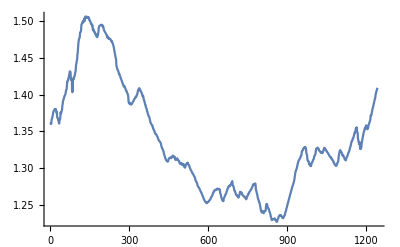

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

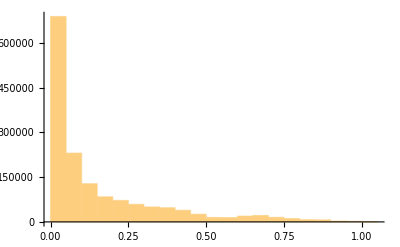

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

```mathematica
Mean[Differences[ds["Times"]]]
```

1

```mathematica
f=CorrelationFunction[ds,{1,1242}]
```

TimeSeries[…]

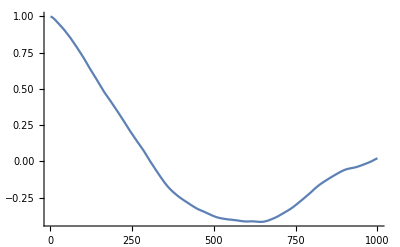

```mathematica
Plot[f[t],{t,1,1000},PlotRange->All]
```

```mathematica
FindRoot[f[t],{t,1}]
```

{t→305.726}

This is equivalent to the original estimate of the lag!

```mathematica
embedLag=RQAEstimateLag[ds]
```

305.726

```mathematica
RQAEstimateDimensionality[ds,embedLag]
```

4.72984×10^-7

{Null,{{{2,0.35251,1262,4.72984×10^-8,956,1.38088×10^-6},{3,0.0661538,956,1.38088×10^-6,650,2.69822×10^-6},{4,0.0116279,650,2.69822×10^-6,344,4.23066×10^-6}}}}

RQATimeSeriesEpochs[ts_,wid_,overlap_]:=
Table[TimeSeriesWindow[ts,{t0,t0+wid}],{t0,ts[“FirstTime”],ts[“LastTime”]-wid,overlap}]

```mathematica
e=RQATimeSeriesEpochs[dsw,200,50]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
Head[%]
```

List

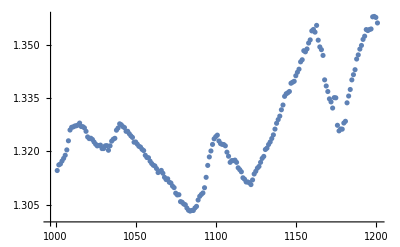

```mathematica
ListPlot[e[[-1]]]
```

If TimeSeriesEpochs defines the windows, how do you talk to the windows, compute the RQA, plot them?

So for each part of list e, calculate the following, with ds replaced by that part of the list:

```mathematica
embedding=RQAEmbed[e[[-1]],3,lag]
```

TimeSeries[…]

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
RQARecurrence[rm]//N
```

0.621731

```mathematica
RQADeterminism[rm]//N
```

0.997235

```mathematica
RQALaminarity[rm,3]//N
```

0.997334

```mathematica
RQATrappingTime[rm]//N
```

42.1375

```mathematica
RQATrend[rm]//N
```

-226.382

```mathematica
RQAEntropy[rm]//N
```

6.03963

```mathematica
RQAChaos[rm]//N
```

0.00555556

```mathematica
RQADmax[rm,2]//N
```

180.

```mathematica
RQAVmax[rm,2]//N
```

120.

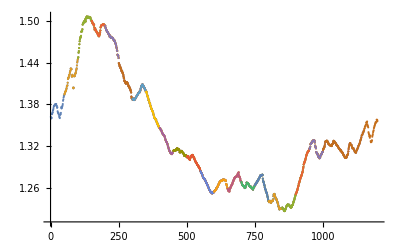
Map[-Graphics-]

```mathematica
Map[ListPlot[e]]
```

```mathematica
len=Length[e]
```

21

```mathematica
e[[3]]//N
```

TimeSeries[…]

```mathematica
Do[ListPlot[e[[i]]],{i,21}]
```

```mathematica
Do[ListPlot[e[[i]]],{i,len}]
```

```mathematica
ListPlot[e[[len]]]
```

-Graphics-

for each part of list e you need to calculate:
1. RQAEmbed[e[[part]],3,lag]
2. RQARecurrenceMap[RQAEmbed[e[[part]],3,lag]]
3. all the RQAs

```mathematica
embedding=RQAEmbed[e[[-1]],3,lag]
```

TimeSeries[…]

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
Table[{RQAVmax[rm,2]//N},{i,10}]
```

{{120.},{120.},{120.},{120.},{120.},{120.},{120.},{120.},{120.},{120.}}

```mathematica
Table[{RQAVmax[RQARecurrenceMap[RQAEmbed[e[[1]],3,lag]],2]//N},{i,10}]
```

{{107.},{107.},{107.},{107.},{107.},{107.},{107.},{107.},{107.},{107.}}

copied from Flip Phillips epochs for alison.nb

```mathematica
eps=RQATimeSeriesEpochs[dsw,200,50]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

So this estimates the lag for each of the time series, eps
Mappaclet:ref/Map[f,expr] or f/@expr
applies f to each element on the first level in expr.

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{68.1693,70.2085,69.0698,68.3119,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709}

```mathematica
Mean[%]
```

72.6888

RQAEmbed::usage=”RQAEmbed[ts,dims,tau] but why.”
#   Slot
represents the first argument supplied to a pure function.

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps];
```

```mathematica
maps=RQADistanceMap/@embeds;
```

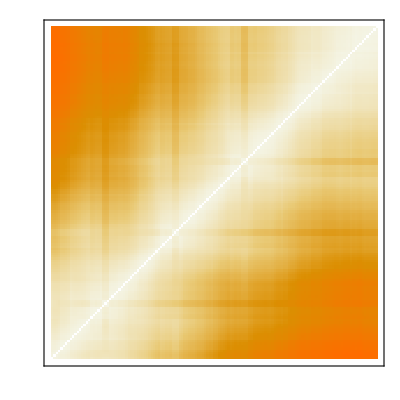
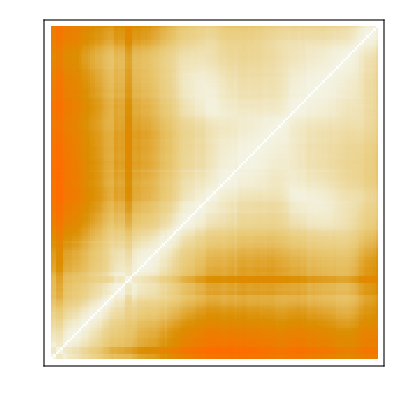
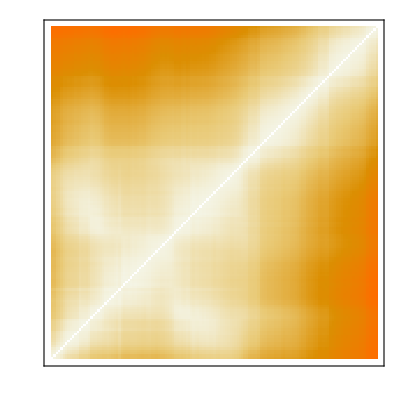
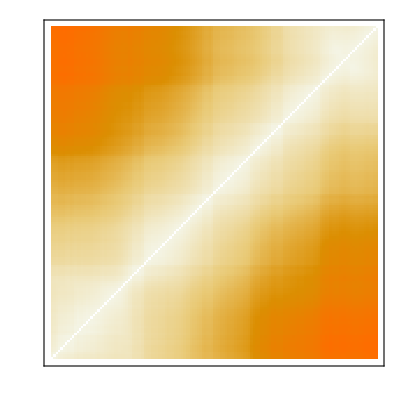
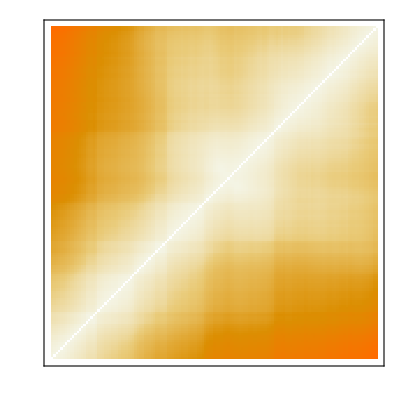
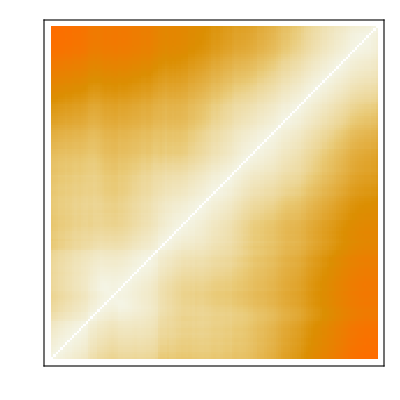
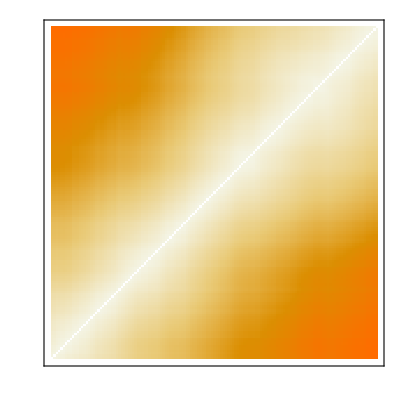
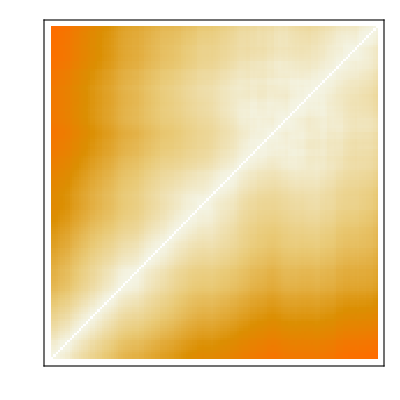

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None]&/@maps
```

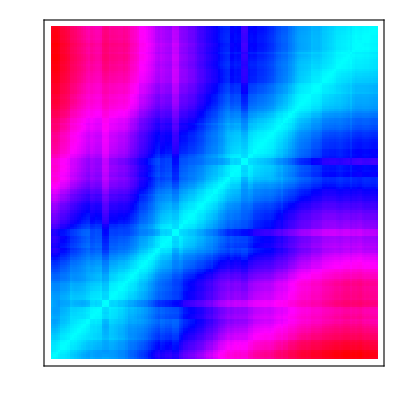
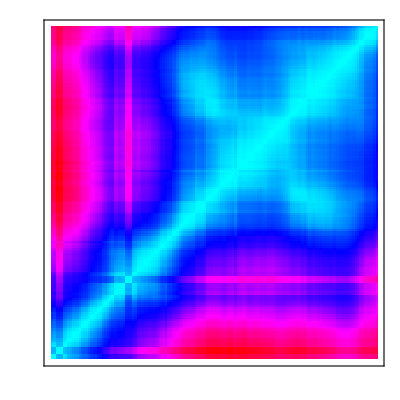
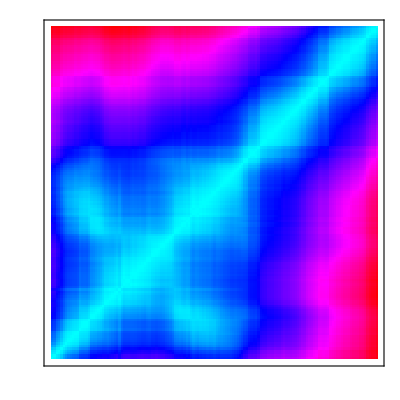
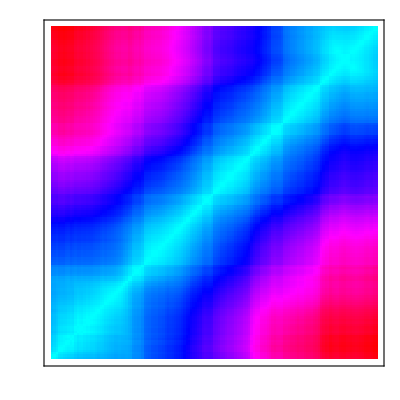
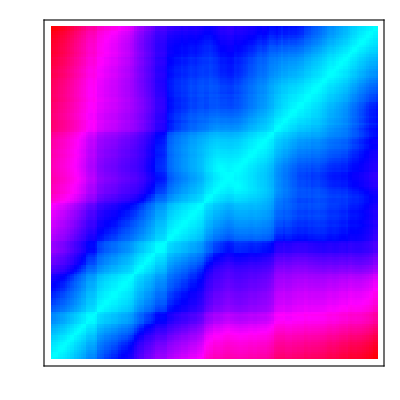
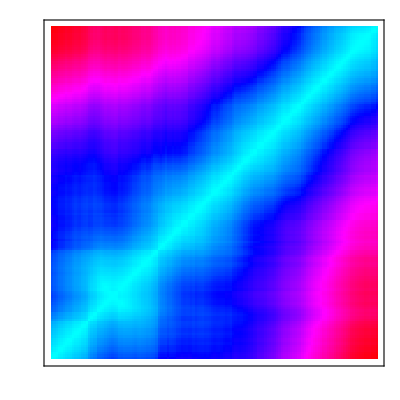
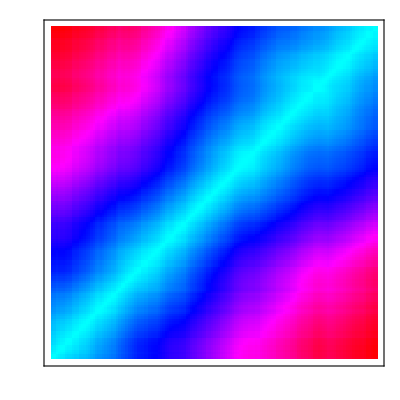
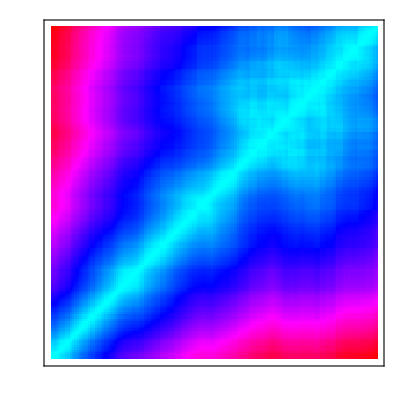

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@maps
```

```mathematica
tables=N[RQADeterminism[eps]]/@embeds
```

{RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]],RQADeterminism[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}][TimeSeries[…]]}

```mathematica
MatrixForm[tables]
```

(RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]]
RQADeterminism[TimeSeries[…]])